```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/";
```

```mathematica
SISF=Table[Import[StringJoin[saveFolder,"SISF_N4096_p3.8000_T0.00337100_waitingTime3162.270000_idx",ToString[i],".nc"],"Data"],{i,0,2}];
```

```mathematica
SISF[[1,2,1]]
```

1.

```mathematica
chi4con=Table[4096*Table[Variance[Table[{SISF[[i,type,t]]},{i,3}]],{t, Length[SISF[[1,1]]]}],{type,2}];
```

```mathematica
ListLogPlot[Table]
```

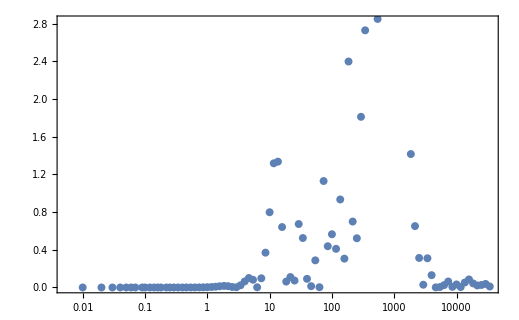

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4[[i,1]]},{i,Length[chi4]}]]
```

```mathematica
Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4[[i,1]]},{i,Length[chi4]}]
```

{{0.,0.},{0.01,8.02134×10^-15},{0.02,1.31677×10^-13},{0.03,6.83581×10^-13},{0.04,2.21385×10^-12},{0.05,5.53415×10^-12},{0.06,1.17408×10^-11},{0.07,2.2236×10^-11},{0.09,6.33414×10^-11},{0.1,9.84414×10^-11},{0.12,2.11562×10^-10},{0.14,4.044×10^-10},{0.16,7.08687×10^-10},{0.18,1.1609×10^-9},{0.22,2.67206×10^-9},{0.25,4.50369×10^-9},{0.29,8.12722×10^-9},{0.34,1.48437×10^-8},{0.4,2.60472×10^-8},{0.46,3.94455×10^-8},{0.54,5.62283×10^-8},{0.63,6.53641×10^-8},{0.74,5.62074×10^-8},{0.86,3.92551×10^-8},{1.,6.92247×10^-8},{1.17,2.27953×10^-7},{1.36,4.75769×10^-7},{1.58,5.94683×10^-7},{1.85,2.66297×10^-7},{2.15,4.8991×10^-7},{2.51,4.77458×10^-6},{2.93,0.0000136686},{3.41,0.0000181761},{3.98,0.0000148607},{4.64,0.0000137619},{5.41,0.000018468},{6.31,0.0000580868},{7.36,0.000120023},{8.58,0.000211203},{10.,0.000287838},{11.66,0.000152702},{13.59,0.0000615777},{15.85,0.0000309974},{18.48,4.18446×10^-6},{21.54,0.0000705768},{25.12,0.000261813},{29.29,0.000336274},{34.15,0.000412212},{39.81,0.000209167},{46.42,0.000016417},{54.12,0.0000183319},{63.1,0.000195928},{73.56,0.000133019},{85.77,0.0000255614},{100.,0.0000568563},{116.59,0.000344946},{135.94,0.00018808},{158.49,0.000402887},{184.78,0.000460515},{215.44,0.000333054},{251.19,0.0000575872},{292.86,0.000532464},{341.45,0.000115582},{398.11,0.000237543},{464.16,1.55343×10^-6},{541.17,0.000108942},{630.96,0.000217138},{735.64,0.00034638},{857.7,0.0000963525},{1000.,0.0000654056},{1165.91,0.000416384},{1359.36,3.30204×10^-6},{1584.89,0.0000176096},{1847.85,2.08907×10^-7},{2154.43,0.000166305},{2511.89,0.0000138395},{2928.64,0.0000917718},{3414.55,0.0000519381},{3981.07,0.0000365602},{4641.59,3.53335×10^-6},{5411.7,6.30842×10^-6},{6309.57,1.60209×10^-6},{7356.42,0.0000117779},{8576.96,9.11692×10^-7},{10000.,0.0000142557},{11659.1,1.54464×10^-9},{13593.6,6.72863×10^-7},{15848.9,9.77251×10^-6},{18478.5,0.0000169344},{21544.3,0.0000117065},{25118.9,5.69418×10^-6},{29286.4,3.78768×10^-6}}

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/chi4CRchi4_N4096_p3.8000_T0.00337100_waitingTime3162.270000_idx1.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/glassyDynamics_N4096_p3.8000_T0.00337100_waitingTime1.000000_idx2.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[<95,8192>, Real64],/postion→NumericArray[<95,8192>, Real64],/time→NumericArray[…],/type→NumericArray[<95,4096>, Integer32],/velocity→NumericArray[<95,8192>, Real64]|>

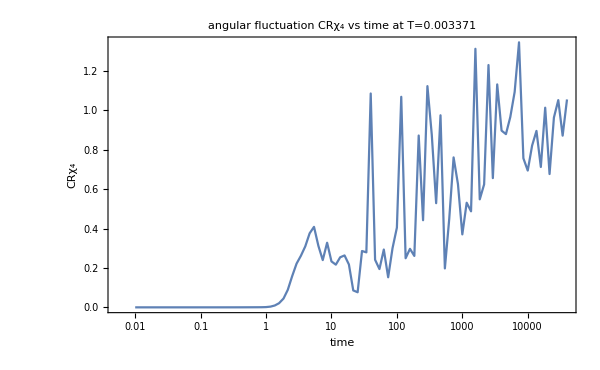

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],data[[2,i]]},{i,Length[data[[1]]]-1}],FrameLabel->{"time","CRχ_4"},ImageSize->600,PlotLabel->"angular fluctuation CRχ_4 vs time at T=0.003371",Joined->True]
```

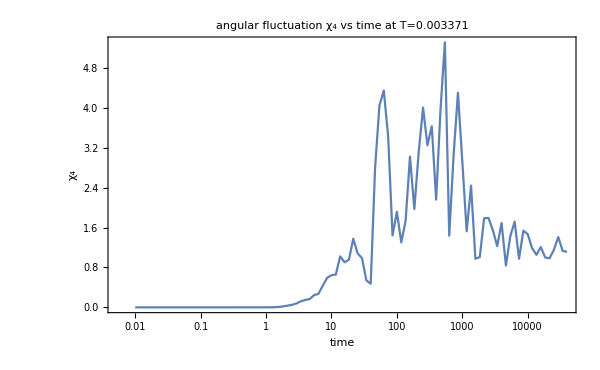

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],data[[1,i]]},{i,Length[data[[1]]]-1}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"angular fluctuation χ_4 vs time at T=0.003371",Joined->True]
```

```mathematica
chi4ang=Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/chi4CRchi4_N4096_p3.8000_T0.00337100_waitingTime3162.270000_idx"<>ToString[idx]<>".nc","Data"][[type]],{idx,0,2}],{type,2}];
```

```mathematica
Table[Mean[Table[chi4ang[[1,idx,i]],{idx,3}]],{i,Length[chi4ang[[1,1]]]}]
```

{0.,-9.74675×10^-11,1.18007×10^-9,6.03071×10^-9,1.9138×10^-8,4.67697×10^-8,9.5898×10^-8,1.76903×10^-7,4.74575×10^-7,7.17667×10^-7,1.46123×10^-6,2.65557×10^-6,4.43788×10^-6,6.95684×10^-6,0.0000148255,0.0000238352,0.0000410223,0.0000725554,0.00012798,0.000205383,0.000345978,0.000556689,0.000888264,0.00134522,0.00204169,0.00323724,0.00518856,0.00847449,0.0148779,0.0268434,0.0466551,0.0707078,0.0905213,0.0988293,0.10838,0.147065,0.251649,0.323482,0.3741,0.368236,0.567664,0.929225,0.924667,0.724678,1.44723,1.52477,2.40342,3.34513,2.03459,2.18821,3.36981,3.74842,3.9531,2.9478,2.64037,3.10744,5.24293,5.58432,4.11441,2.83943,3.13753,2.97566,4.01251,3.68818,4.52238,5.90027,2.83114,3.01812,3.31592,3.46198,3.35078,1.74096,1.54315,2.04779,1.97227,1.74658,1.85096,1.37519,1.53502,1.13461,1.60701,1.34348,1.13693,1.1546,1.24475,1.15129,1.17217,1.1081,0.928707,1.02952,1.0676,1.14237,0.978538}

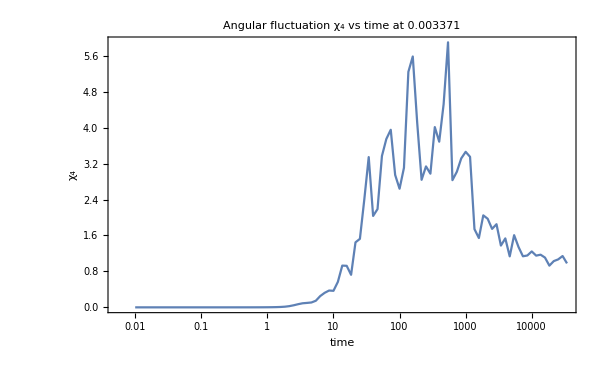

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],Mean[Table[chi4ang[[1,idx,i]],{idx,3}]]},{i,Length[chi4ang[[1,1]]]}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"Angular fluctuation χ_4 vs time at 0.003371",Joined->True]
```

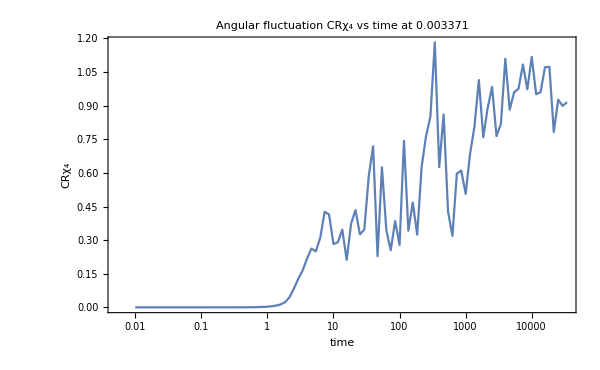

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],Mean[Table[chi4ang[[2,idx,i]],{idx,3}]]},{i,Length[chi4ang[[1,1]]]}],FrameLabel->{"time","CRχ_4"},ImageSize->600,PlotLabel->"Angular fluctuation CRχ_4 vs time at 0.003371",Joined->True]
```

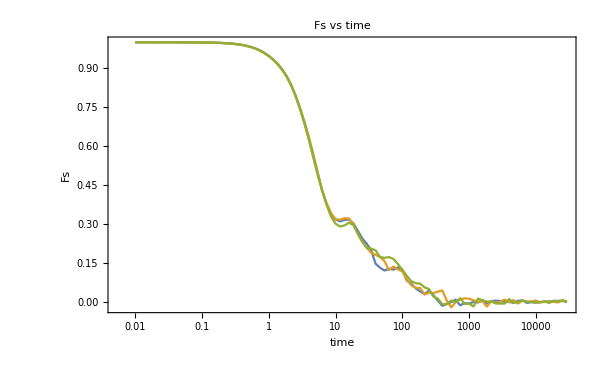

```mathematica
ListLogLinearPlot[Table[Table[{N[test[[4,i,1]]-test[[4,1,1]]],SISF[[idx,1,i]]},{i,Length[chi4]-1}],{idx,3}],FrameLabel->{"time","Fs"},ImageSize->600,PlotLabel->"Fs vs time",Joined->True]
```

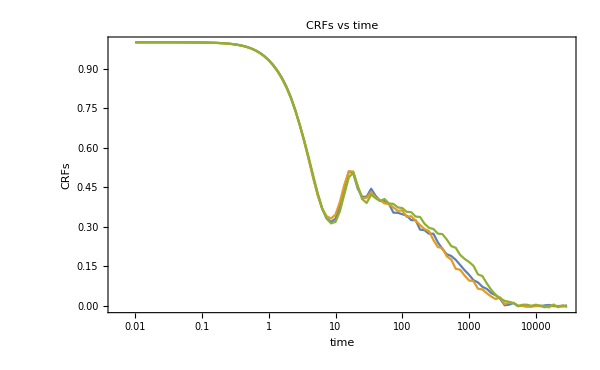

```mathematica
ListLogLinearPlot[Table[Table[{N[test[[4,i,1]]-test[[4,1,1]]],SISF[[idx,2,i]]},{i,Length[chi4]-1}],{idx,3}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True]
```

```mathematica
chi4con[[1]]
```

{{0.},{6.18124×10^-11},{9.8715×10^-10},{4.98631×10^-9},{1.57185×10^-8},{3.82576×10^-8},{7.90457×10^-8},{1.45852×10^-7},{3.94914×10^-7},{5.98852×10^-7},{1.22813×10^-6},{2.24815×10^-6},{3.78605×10^-6},{5.98302×10^-6},{0.0000129768},{0.0000211502},{0.0000370643},{0.0000669677},{0.000120789},{0.000197308},{0.000336182},{0.000534724},{0.000801931},{0.00105702},{0.00124879},{0.0014457},{0.00202605},{0.00330206},{0.00477603},{0.00575169},{0.00837283},{0.0216051},{0.0620073},{0.125762},{0.175138},{0.125563},{0.00384263},{0.042961},{0.2058},{0.36917},{0.766022},{0.854786},{0.319303},{0.0506831},{0.202058},{0.195501},{0.354228},{0.282512},{2.81721},{2.32422},{2.64311},{3.13755},{1.85012},{0.469138},{0.0594525},{0.39006},{0.258876},{0.495324},{0.898987},{0.990435},{0.202505},{0.183411},{1.39449},{4.36681},{0.226105},{0.781471},{0.119367},{0.900067},{0.536766},{0.503319},{0.61415},{0.265458},{0.0128516},{0.381657},{0.00491195},{0.142762},{0.118258},{0.239604},{0.179177},{0.160584},{0.117731},{0.0018662},{0.0288117},{0.00810861},{0.0876221},{0.00231411},{0.00966412},{0.0487067},{0.0260891},{0.0410422},{0.0238011},{0.0204108},{0.00791781}}

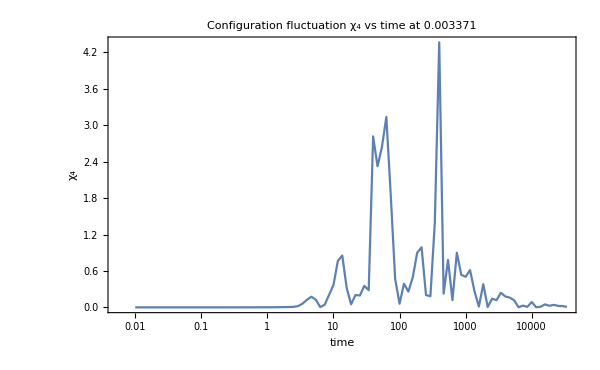

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4con[[1,i,1]]},{i,Length[chi4con[[1]]]}],FrameLabel->{"time","χ_4"},ImageSize->600,PlotLabel->"Configuration fluctuation χ_4 vs time at 0.003371",Joined->True,PlotRange->All]
```

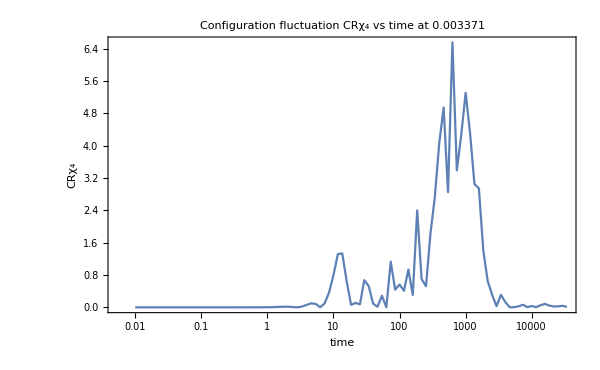

```mathematica
ListLogLinearPlot[Table[{N[test[[4,i,1]]-test[[4,1,1]]],chi4con[[2,i,1]]},{i,Length[chi4con[[1]]]}],FrameLabel->{"time","CRχ_4"},ImageSize->600,PlotLabel->"Configuration fluctuation CRχ_4 vs time at 0.003371",Joined->True,PlotRange->All]
```

```mathematica
N[test[[4,1,1]]]
```

0.

```mathematica
N[84914/3600]
```

23.5872

```mathematica
N[64*2000000/1024/1024/1024]
```

0.119209

```mathematica
N[147815/60/60]
```

41.0597